```mathematica
urchinCckDcPageviews:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-CCK-DC-by-day.csv"]]
```

```mathematica
urchinAboutIndex:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-about-index-pageviews.csv"]]
```

```mathematica
urchinAboutLicensing:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-about-licensing-pageviews.csv"]]
```

```mathematica
urchinFullInstall:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-get-phet-full-install-pageviews.csv"]]
```

```mathematica
urchinJohnTravoltage:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-john-travoltage-pageviews.csv"]]
```

```mathematica
urchinBytes:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-bytes-by-day.csv"]]
```

```mathematica
urchinHits:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-hits-by-day.csv"]]
```

```mathematica
urchinIndexPageviews:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-index-pageviews.csv"]]
```

```mathematica
urchinPageviews:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-pageviews-by-day.csv"]]
```

```mathematica
urchinSessions:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-sessions-by-day.csv"]]
```

```mathematica
urchinLoginRedirectPageviews:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-teacher-ideas-login-and-redirect-pageviews-by-day.csv"]]
```

```mathematica
urchinProjectileMotionSWF:=Flatten[Import["/home/jon/phet/svn/trunk/team/jolson/stats/urchin/p/urchin-1yr-projectile-motion-swf.csv"]]
```

```mathematica
days:=(#[[1]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-index-pageviews.csv"]
```

```mathematica
analyticsIndexPageviews:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-index-pageviews.csv"]
```

```mathematica
analyticsPageviews:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-pageviews-by-day.csv"]
```

```mathematica
analyticsCckDcPageviews:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-pageviews-CCK-DC-by-day.csv"]
```

```mathematica
analyticsVisits:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-visits-by-day.csv"]
```

```mathematica
analyticsAboutIndex:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-about-index-pageviews.csv"]
```

```mathematica
analyticsAboutLicensing:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-about-licensing-pageviews.csv"]
```

```mathematica
analyticsFullInstall:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-get-phet-full-install-pageviews.csv"]
```

```mathematica
analyticsJohnTravoltage:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-john-travoltage-pageviews.csv"]
```

```mathematica
analyticsProjectileMotionAllHTML:=(#[[2]]&)/@Import["/home/jon/phet/svn/trunk/team/jolson/stats/analytics/p/analytics-projectile-motion-all-html.csv"]
```

```mathematica
dates:={{2008,9,1},{2008,10,1},{2008,11,1},{2008,12,1},{2009,1,1},{2009,2,1},{2009,3,1},{2009,4,1},{2009,5,1},{2009,6,1},{2009,7,1},{2009,8,1}}
```

```mathematica
testplot:=DateListPlot[{urchinSessions,analyticsVisits},{{2008,8,11},Automatic,"Day"},Joined->True,AspectRatio->0.1,ImageSize->{1000,200},FrameTicks->{{Automatic,Automatic},{dates,Automatic}},DateTicksFormat->{"MonthNameShort"," ","YearShort"}]
```

```mathematica
opts:={Joined->True,AspectRatio->0.1,ImageSize->{1000,200},FrameTicks->{{Automatic,Automatic},{dates,Automatic}},DateTicksFormat->{"MonthNameShort"," ","YearShort"}}
```

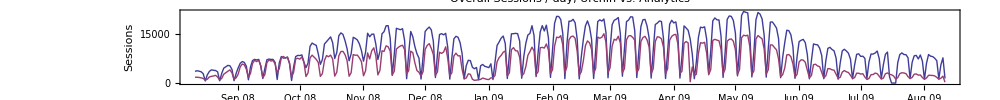

```mathematica
DateListPlot[{urchinSessions,analyticsVisits},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"Overall Sessions / day, Urchin vs. Analytics",FrameLabel->{"Day","Sessions"}]
```

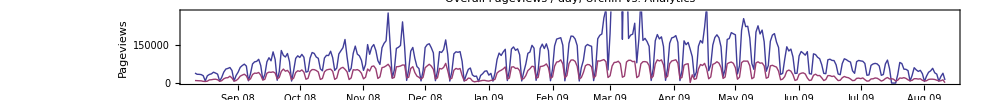

```mathematica
DateListPlot[{urchinPageviews,analyticsPageviews},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"Overall Pageviews / day, Urchin vs. Analytics",FrameLabel->{"Day","Pageviews"}]
```

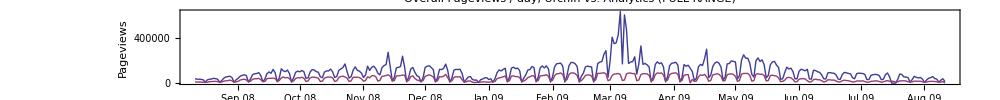

```mathematica
DateListPlot[{urchinPageviews,analyticsPageviews},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"Overall Pageviews / day, Urchin vs. Analytics (FULL RANGE)",FrameLabel->{"Day","Pageviews"},PlotRange->{Automatic, {0,All}}]
```

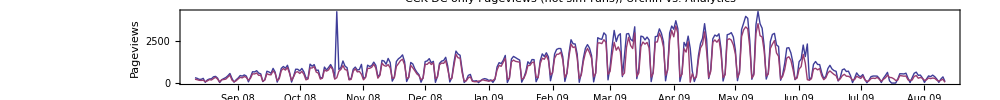

```mathematica
DateListPlot[{urchinCckDcPageviews,analyticsCckDcPageviews},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"CCK DC only Pageviews (not sim-runs), Urchin vs. Analytics",FrameLabel->{"Day","Pageviews"}]
```

```mathematica
Total[urchinCckDcPageviews]
```

405172

```mathematica
Total[analyticsCckDcPageviews]
```

339266

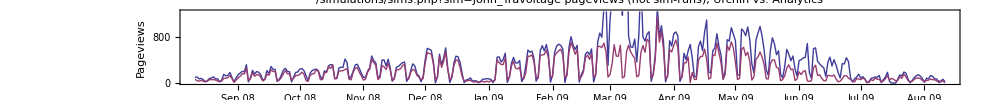

```mathematica
DateListPlot[{urchinJohnTravoltage,analyticsJohnTravoltage},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/simulations/sims.php?sim=John_Travoltage pageviews (not sim-runs), Urchin vs. Analytics",FrameLabel->{"Day","Pageviews"}]
```

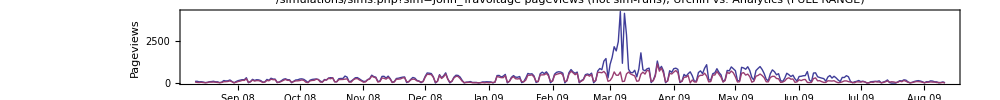

```mathematica
DateListPlot[{urchinJohnTravoltage,analyticsJohnTravoltage},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/simulations/sims.php?sim=John_Travoltage pageviews (not sim-runs), Urchin vs. Analytics (FULL RANGE)",FrameLabel->{"Day","Pageviews"},PlotRange->{Automatic, {0,All}}]
```

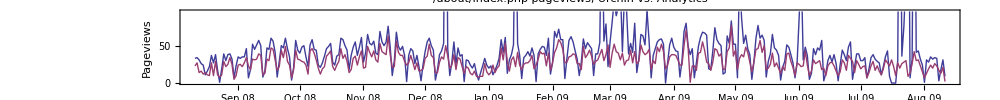

```mathematica
DateListPlot[{urchinAboutIndex,analyticsAboutIndex},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/about/index.php pageviews, Urchin vs. Analytics",FrameLabel->{"Day","Pageviews"}]
```

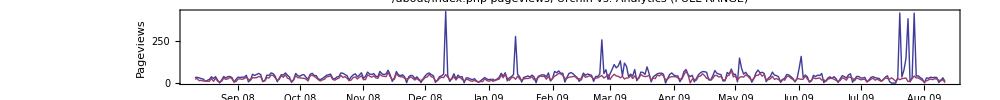

```mathematica
DateListPlot[{urchinAboutIndex,analyticsAboutIndex},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/about/index.php pageviews, Urchin vs. Analytics (FULL RANGE)",FrameLabel->{"Day","Pageviews"},PlotRange->{Automatic, {0,All}}]
```

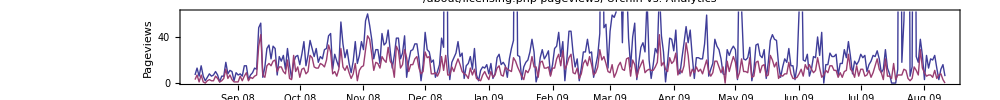

```mathematica
DateListPlot[{urchinAboutLicensing,analyticsAboutLicensing},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/about/licensing.php pageviews, Urchin vs. Analytics",FrameLabel->{"Day","Pageviews"}]
```

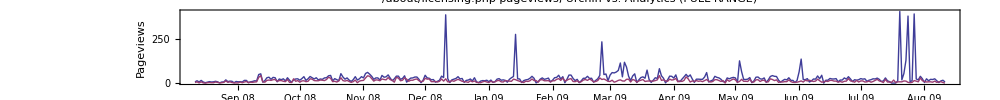

```mathematica
DateListPlot[{urchinAboutLicensing,analyticsAboutLicensing},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/about/licensing.php pageviews, Urchin vs. Analytics (FULL RANGE)",FrameLabel->{"Day","Pageviews"},PlotRange->{Automatic, {0,All}}]
```

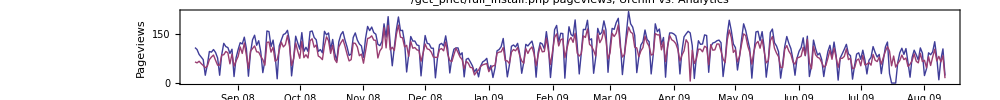

```mathematica
DateListPlot[{urchinFullInstall,analyticsFullInstall},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"/get_phet/full_install.php pageviews, Urchin vs. Analytics",FrameLabel->{"Day","Pageviews"}]
```

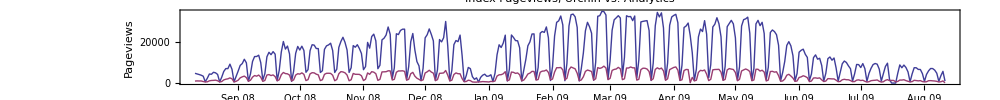

```mathematica
DateListPlot[{urchinIndexPageviews,analyticsIndexPageviews},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"Index Pageviews, Urchin vs. Analytics",FrameLabel->{"Day", "Pageviews"}]
```

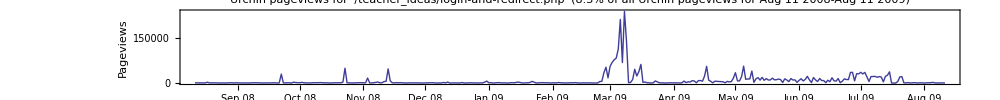

```mathematica
DateListPlot[urchinLoginRedirectPageviews,{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"Urchin pageviews for '/teacher_ideas/login-and-redirect.php' (8.3% of all Urchin pageviews for Aug 11 2008-Aug 11 2009)",FrameLabel->{"Day", "Pageviews"},PlotRange->{Automatic,{0,All}}]
```

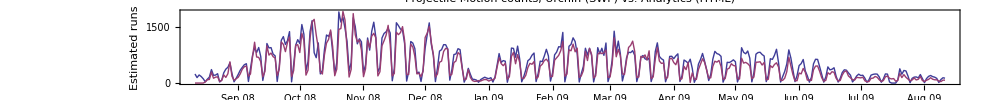

```mathematica
DateListPlot[{urchinProjectileMotionSWF,analyticsProjectileMotionAllHTML},{{2008,8,11},Automatic,"Day"},opts,PlotLabel->"Projectile Motion counts, Urchin (SWF) vs. Analytics (HTML)",FrameLabel->{"Day", "Estimated runs"}]
```

```mathematica
Total[urchinProjectileMotionSWF]
```

201045

```mathematica
Total[analyticsProjectileMotionAllHTML]
```

173774